# Multiscale spatiotemporal Lorenz 96 system

#### This Lorenz 96 system has three tiers of nonlinearly interacting variables representing slow/large - scale (X), intermediate (Y), and fast/small - scale (Z) processes . Which AI-based data-driven technique(s) can best predict the spatiotemporal evolution of a multiscale chaotic system, when only the slow/large-scale variables are known (during training) and are of interest (to predict during testing)? We emphasize that, unlike many other studies, our focus is not on reproducing long-term statistics of the underlying dynamical system (al- though that will be examined too) but on predicting the short- term trajectory from a given initial condition.

#### or

#### This set of coupled nonlinear ordinary differential equa- tions (ODEs) is a three-tier extension of Lorenz’s original model (Lorenz, 1996) and has been proposed by Thornes et al. (2017) as a fitting prototype for multiscale chaotic variability of the weather and climate system and a useful test bed for novel methods. In these equations, F = 20 is a large-scale forcing that makes the system highly chaotic, andb=c=e=d=g=10andh=1aretunedtoproduce appropriate spatiotemporal variability of the three variables (see below). The indices are i,j,k = 1,2,...8; thus X has 8 elements while Y and Z have 64 and 512 elements, respectively. In the context of atmospheric circulation, the slow variable X can represent the low-frequency variability of the large-scale circulation, while the intermediate variable Y and fast variable Z can represent synoptic and baroclinic eddies and small- scale convection, respectively.

#### The Lorenz 96 model is a dynamical system formulated by Edward Lorenz in 1996.[1] It is defined as follows. For {\displaystyle i=1,...,N}i=1,...,N: {\displaystyle {\frac {dx_{i}}{dt}}=(x_{i+1}-x_{i-2})x_{i-1}-x_{i}+F}{\displaystyle {\frac {dx_{i}}{dt}}=(x_{i+1}-x_{i-2})x_{i-1}-x_{i}+F} where it is assumed that {\displaystyle x_{-1}=x_{N-1},x_{0}=x_{N}}{\displaystyle x_{-1}=x_{N-1},x_{0}=x_{N}} and {\displaystyle x_{N+1}=x_{1}}{\displaystyle x_{N+1}=x_{1}} and {\displaystyle N\geq 4}{\displaystyle N\geq 4}. Here {\displaystyle x_{i}}x_{i} is the state of the system and {\displaystyle F}F is a forcing constant. {\displaystyle F=8}F=8 is a common value known to cause chaotic behavior.

#### Ed Lorenz was a genius at coming up with simple models that capture the essence of a problem in a much more complex system. His famous butterfly model from 1963 jump-started chaos research, followed by more sophisticated models to describe upscale error growth (1969) and the general circulation of the atmosphere (1984). In 1995, he created another chaotic mode that shall be the topic of this blog post. Confusingly, even though the original paper appeared in 1995, most people refer to the model as the Lorenz 96 (L96) model, which we will also do here.

```mathematica
s = NDSolve[{Derivative[1][x][t] == -3 (x[t] - y[t]), 
    Derivative[1][y][t] == -x[t] z[t] + 26.5 x[t] - y[t], 
    Derivative[1][z][t] == x[t] y[t] - z[t], x[0] == z[0] == 0, 
    y[0] == 1}, {x, y, z}, {t, 0, 400}, MaxSteps -> ∞];
Show[ParametricPlot3D[Evaluate[{x[t], y[t], z[t]} /. s], {t, 0, 400}, 
  PlotPoints -> 1000, 
  PlotStyle -> Directive[Thick, RGBColor[.8, 0, 0]], 
  ColorFunction -> (ColorData["SolarColors", #4] &)], 
 Graphics3D[{ColorData["SolarColors"][0], 
   Sphere[First[({x[t], y[t], z[t]} /. s) /. t -> 0], .75]}], 
 RotationAction -> "Clip", Boxed -> False, SphericalRegion -> False, 
 Axes -> False, ImageSize -> 500]
```

```mathematica
Ω = 
  Polygon[2 {{-Pi, -E}, {0, -1}, {0, 0}, {Pi, 0}, {Pi, E}, {-Pi, 
      E}}];
NDSolve[{Laplacian[
      u[x, y], {x, y}] + λ Cos[v[x, y]]  Sin[u[x, y]] == 0 , 
   Laplacian[
      v[x, y], {x, y}] + λ Sin[u[x, y] ] Sin[v[x, y]] == 0, 
   DirichletCondition[{u[x, y] == 1/10, v[x, y] == 1/20}, 
    True]} /. λ -> 5, {u, 
  v}, {x, y} ∈ Ω]
```

```mathematica
Join[Table[(x[i])'[t]==-x[i-1][t]*(x[i-2][t]-x[i+1][t])-x[i][t]+F,{i,1,10}],
{x[0][t]==x[10][t],x[-1][t]==x[9][t]}]
```

{x[1]'[t]==10-x[1][t]-x[0][t] (x[-1][t]-x[2][t]),x[2]'[t]==10-x[2][t]-x[1][t] (x[0][t]-x[3][t]),x[3]'[t]==10-x[3][t]-x[2][t] (x[1][t]-x[4][t]),x[4]'[t]==10-x[4][t]-x[3][t] (x[2][t]-x[5][t]),x[5]'[t]==10-x[5][t]-x[4][t] (x[3][t]-x[6][t]),x[6]'[t]==10-x[6][t]-x[5][t] (x[4][t]-x[7][t]),x[7]'[t]==10-x[7][t]-x[6][t] (x[5][t]-x[8][t]),x[8]'[t]==10-x[8][t]-x[7][t] (x[6][t]-x[9][t]),x[9]'[t]==10-x[9][t]-x[8][t] (x[7][t]-x[10][t]),x[10]'[t]==10-x[10][t]-x[9][t] (x[8][t]-x[11][t]),x[0][t]==x[10][t],x[-1][t]==x[9][t]}

```mathematica
n=36;
F=10;
toString[i_]:=ToString[If[i==-1,n-1,If[i==0,n,If[i==n+1,1,i]]]];
ClearAll[t]
equation=ToExpression[Join[Table["x"<>ToString[i]<>"'[t]==(x"<>toString[i+1]<>"[t]-x"<>toString[i-2]<>"[t])*x"<>toString[i-1]<>"[t]-x"<>toString[i]<>"[t]+F",{i,n}],
Table["x"<>ToString[i]<>"[0]==RandomReal[10]",{i,n}]]];
var=ToExpression[Table["x"<>ToString[i],{i,n}]];
```

```mathematica
result=NDSolve[equation,var,{t,0,500}];
```

```mathematica
value=Table[Evaluate[Map[#[t]&,var]/.result],{t,0,400}][[;;,1]];
```

```mathematica
value=value+15;
```

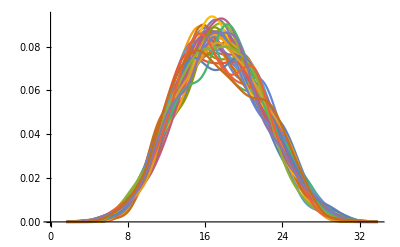

```mathematica
SmoothHistogram[Table[value[[;;,i]],{i,36}]]
```

```mathematica
plot=Table[ListLinePlot[Append[Table[{value[[t,i]]*Cos[angel[[i]]],value[[t,i]]*Sin[angel[[i]]]},{i,Length[angel]}],
	{value[[t,1]]*Cos[angel[[1]]],value[[t,1]]*Sin[angel[[1]]]}],AspectRatio->1,PlotRange->{{-30,30},{-30,30}},Frame->True,ImageSize->300],{t,Length[value]}];
```

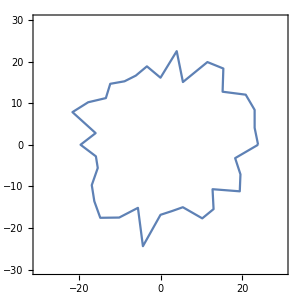
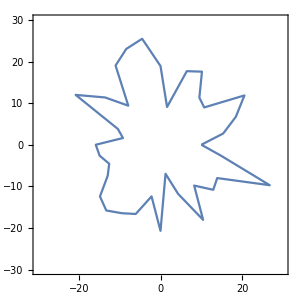
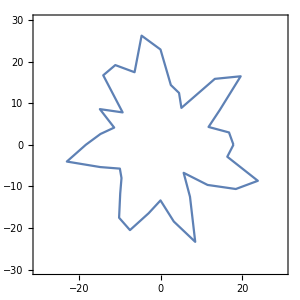

```mathematica
Table[plot[[i]],{i,1,3}]
```

```mathematica
Export["/Users/lambda/Documents/NAS/base.gif",plot];
```